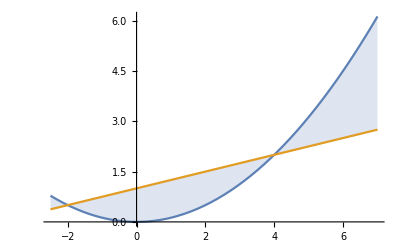

```mathematica
f[y_]=y^2/8;
g[y_]=(y+4)/4;
Plot[{f[y],g[y]},{y,-2.5,7},Filling->{1->{2}}]
```

```mathematica
NSolve[f[y]==g[y]]
```

{{y→-2.},{y→4.}}

```mathematica
Integrate[-f[y]+g[y],{y,-3.58258,5.58258}]
```

2.29127